```mathematica
连接两线圈的线段上电势和电场的分布
```

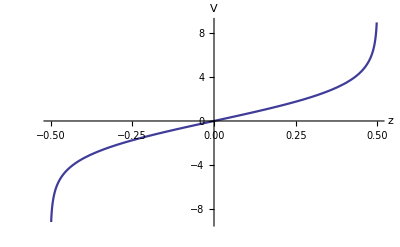

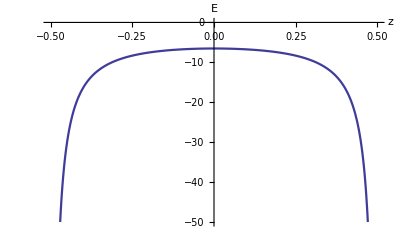

```mathematica
V0[z_,ρ_,R_]:=(2EllipticK[-(2R*ρ)/(z^2+(R-ρ)^2)])/(√(z^2+(R-ρ)^2))+
(2EllipticK[(2R*ρ)/(z^2+(R+ρ)^2)])/(√(z^2+(R+ρ)^2));
V1[z_,ρ_,R_]:=V0[z-d/2,ρ,R];
V2[z_,ρ_,R_]:=-V0[z+d/2,ρ,R];
V[z_,ρ_,R_]:=V1[z,ρ,R]+V2[z,ρ,R];
d=1;R=1;
Plot[V[z,1,1],{z,-d/2,d/2},
AxesLabel->{"z","V"},
AxesStyle->Thickness[0.003],
PlotStyle->Thickness[0.004]]
field=-D[V[z,1,1],z];
Plot[field,{z,-d/2,d/2},AxesLabel->{"z","E"},
PlotRange->{-50,0},AxesStyle->Thickness[0.003],
PlotStyle->Thickness[0.004]]
Clear[V,V0,V1,V2,field,d]
```